## Live evaluation of expressions in TreeForm

### Introduction

This Mathematica notebook is licensed under a  
It is a demonstration that allows a user try values of input to solve an equation displayed in tree form, with the partial values shown at each stage of the calculation.  The idea behind the demonstration is discussed at length in .

The demonstration is a kludge that I made up to show what I was thinking of.   It should be possible to create a Mathematica command EvaluatableTreeForm that would produce a package showing a manipulatable tree form of any Mathematica expression.

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Introductory experiments

```mathematica
Hyperlink["this blog post", "http://sixwingedseraph.wordpress.com/2011/06/23/computable-algebraic-expressions-in-tree-form/"]
```

```mathematica
trf:=TraditionalForm;txf:=TeXForm
```

```mathematica
Solve[4(x-2)==6,x]
```

{{x→7/2}}

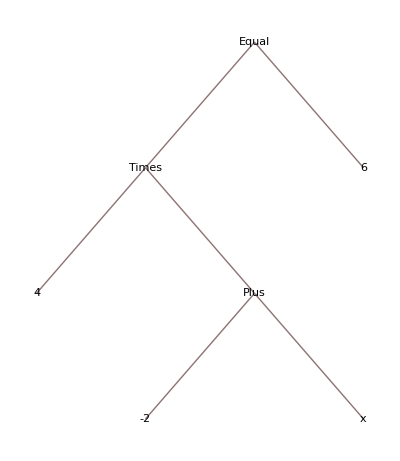

```mathematica
TreeForm[4(x-2)==6]
```

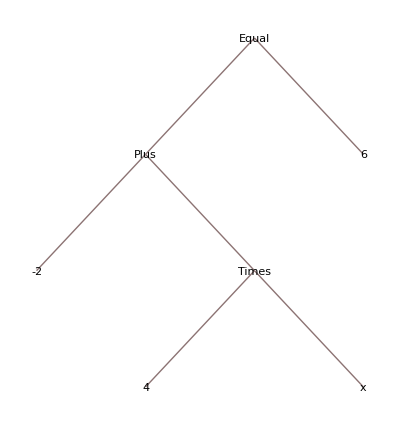

```mathematica
TreeForm[4x-2==6]
```

### Code for the demonstration

```mathematica
nodelabel[e_,f_]:=TableForm[{e,f},TableAlignments->Center]
```

```mathematica
tre[x_]:=TreePlot[{nodelabel[4(x-2)==6,"Equals"]->nodelabel[4(x-2),"Times"],nodelabel[4(x-2)==6,"Equals"]->6,nodelabel[4(x-2),"Times"]->4,nodelabel[4(x-2),"Times"]->nodelabel[x-2,"Plus"],nodelabel[x-2,"Plus"]->x,nodelabel[x-2,"Plus"]-> -2},Top,nodelabel[4(x-2)==6,"Equals"],VertexLabeling->True]
```

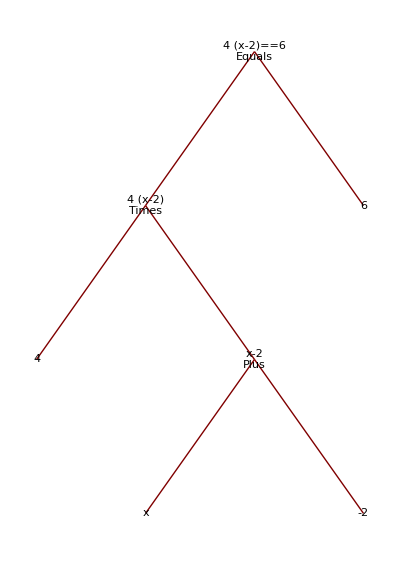

```mathematica
tre[x]
```

### Demonstration

```mathematica
Manipulate[tre[x],{{x,6},-2,6,0.1},SaveDefinitions->True]
```

```mathematica
Manipulate[tre[x],{{x,3.5},-2,6,0.1}]
```